Mats-Erik Pistol

Solid State Physics and NanoLund, 
Lund University, Lund, Sweden

## This section contains the code to construct isospectral sets.

The commands in the following cell are as follows: 
ConnectedGraphs[n] loads all connected graphs with n vertices. n should be at most 7. If n is larger than 7, not all graphs are loaded since they are lacking in Wolframs database.
ConnectedGraphsAll[n] loads all connected graphs with 2 to n vertices. n should be at most 7 to get all graphs.
I think ConnectedGraphs[2;;n] loads all loads all connected graphs with at most n vertices, excluding the single vertex graph. 
PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.
PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added, 0 and n inclusive.
IsospectralPairs[h] returns all tentative isospectral pairs from the list h.
IsospectralPairsFromData[h, tab] returns all tentative isospectral pairs from the list h, but using a precomputed list of roots: tab, probably read from disk.
EulerCharacteristicGraph[h] returns the Euler characteristic for the graph h.
DeterminantD[h] gives the secular determinant, D(k), for the graph h. DeterminantD[mo] is defined in GraphRoots and is used to check multiplicities.

```mathematica
ConnectedGraphs[n_]:=Module[{graphs},graphs=GraphData/@GraphData[n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

ConnectedGraphsAll[n_]:=Module[{graphs},graphs=GraphData/@GraphData[2;;n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

PEA[h_]:=
Module[{tmp},tmp=Table[EdgeAdd[h,i<->VertexCount[h]+1],{i,1,VertexCount[h]}]//Flatten;
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]]

PendantEdgeAdd[h_,n_:1]:=Module[{tmp},tmp=Nest[Flatten@(PEA/@#1)&,{h},n];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]];

PendantEdgeAdd::usage=
"PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.";

PendantEdgeAddAll[h_,n_]:=Module[{tmp},tmp=Flatten@Table[Nest[Flatten@(PEA/@#1)&,{h},i],{i,1,n}];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp∪{h}]];

PendantEdgeAdd::usage=
"PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added.";

IsospectralPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

IsospectralPairsFromData[h_List,tab_]:=
Module[{aaa},aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs];];

EulerCharacteristicGraph[h_Graph]:=VertexCount@h-EdgeCount@h;
```

The following cell gives useful commands to set the current directory and examples how to save computed graphs and eigenfrequencies.

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

/Users/mepistol/People/Mats-Erik/IsospectralGraphs/Mathematica programs

```mathematica
directory="/Users/mepistol/People/Mats-Erik/IsospectralGraphs/Mathematica programs";
SetDirectory[directory];
Directory[]
```

/Users/mepistol/People/Mats-Erik/IsospectralGraphs/Mathematica programs

```mathematica
tab>>"TreeRoots10vertices";
trees>>"Trees10vertices";
```

```mathematica
t=<<"TreeRoots10vertices";
gr=<<"Trees10vertices";
```

```mathematica
tab>>"AllconnectedRoots8vertices";
Allconnected>>"Allconnected8vertices";
```

```mathematica
tab=<<"AllconnectedRoots8vertices";
Allconnected=<<"Allconnected8vertices";
```

## The following section constructs the isospectral pairs in the paper.

First we do it for all connected graphs with at most seven vertices.

```mathematica
Allconnected=ConnectedGraphsAll[7]; (* Here we load all connected graphs with at most 7 vertices *)
```

```mathematica
isospectralpairsconnected=IsospectralPairs[Allconnected]; (* Here we find suspect isospectral pairs. They have to be checked for multiplicity of their roots. *)
```

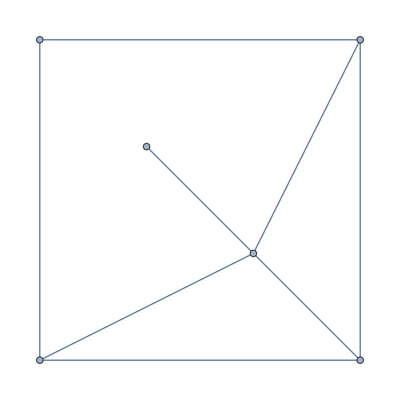
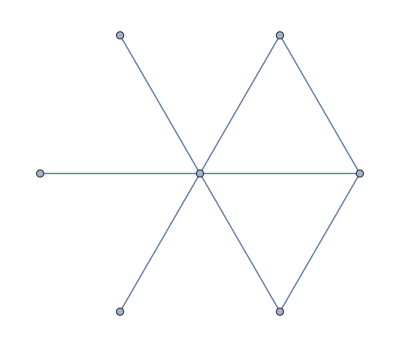
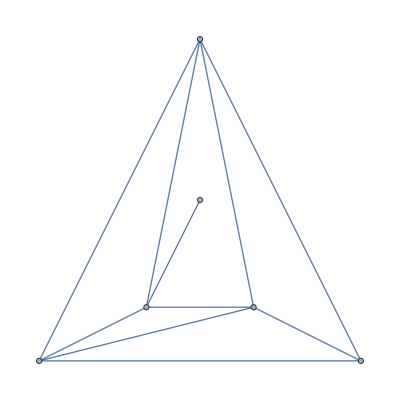
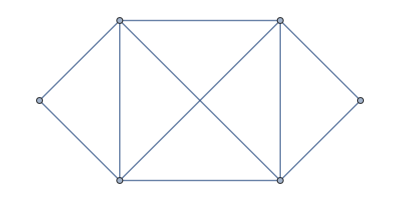
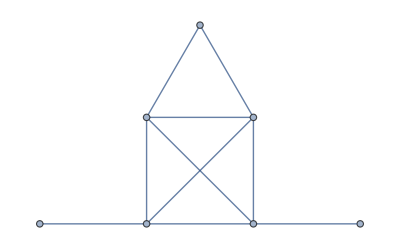
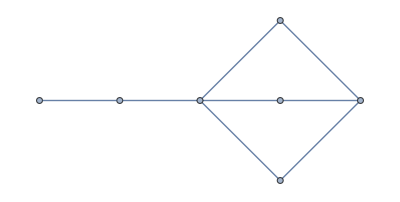
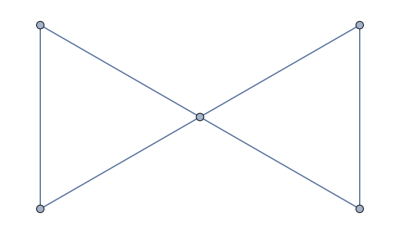
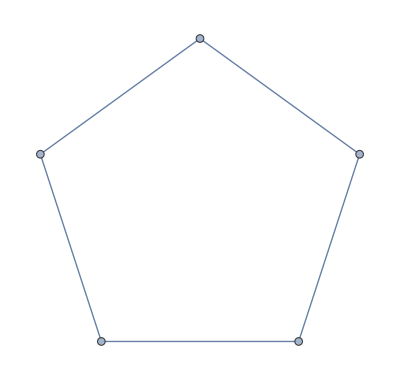
Small[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}]

```mathematica
isospectralpairsconnected//Small (* These are the suspects. Many can immediately be eliminated after checking Euler characteristics or for reasons such as being clearly isomorphic. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//Simplify//Factor  (* We here check for multiplicity. Each pair or set is checked individually. *)
```

{48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/10))^6 (1+ⅇ^((ⅈ k)/10))^4 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5))^3 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+2 ⅇ^((2 ⅈ k)/5)),-64 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/10))^6 (1+ⅇ^((ⅈ k)/10))^4 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5))^3 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+2 ⅇ^((2 ⅈ k)/5)),-32 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/10))^5 (1+ⅇ^((ⅈ k)/10))^3 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5))^2 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+2 ⅇ^((2 ⅈ k)/5))^2}

```mathematica
Finalisospectralpairsconnected={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}; (* These are the final isospectral pairs with at most seven vertices after checking multiplicities. *)
```

```mathematica
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringElectricalEmbedding",ImageSize->70]&]/@Finalisospectralpairsconnected
```

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
(* Plotted with a different embedding. *)
```

Then for trees with at most ten vertices

```mathematica
trees=PendantEdgeAddAll[-Graphics-,8];
```

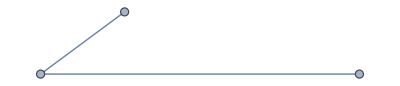
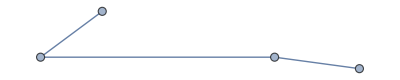
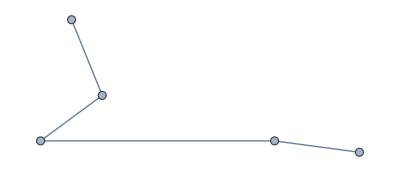
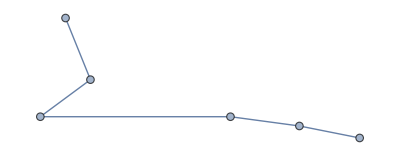
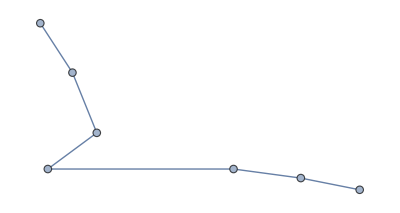
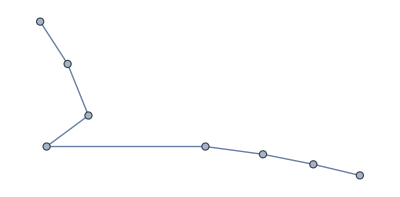
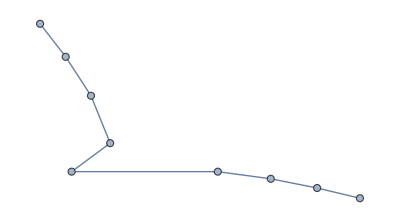
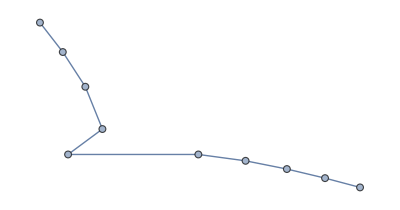
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
suspecttrees=IsospectralPairs[trees]
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify//Factor  (* We here check for multiplicity. Each pair is checked individually. *)
```

{-48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9)),48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9))}

```mathematica
Finalisospectraltrees={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}};
(* The final checked trees with at most ten vertices *)
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringEmbedding",ImageSize->70]&]/@Finalisospectraltrees
```

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* Different embedding. *)
```

Here we do it for trees with twelve vertices.

```mathematica
treesten=PendantEdgeAddAll[-Graphics-,10]; (* Lets do it with up to 12 vertices. This takes a few hours on a laptop. *)
```

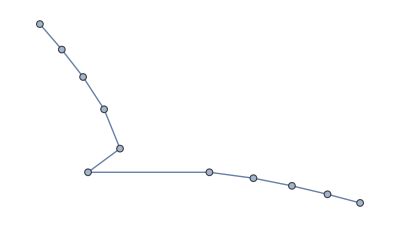
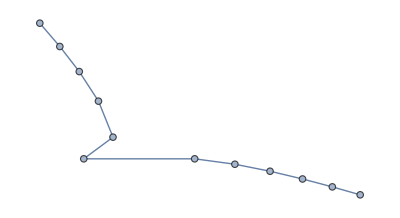
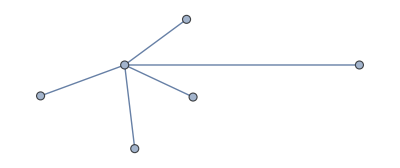
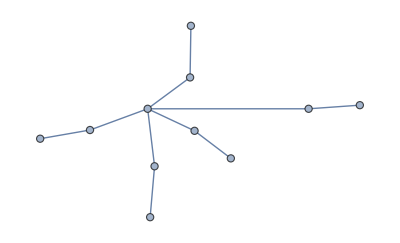
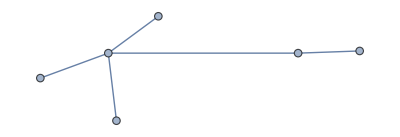
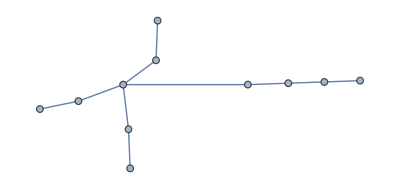
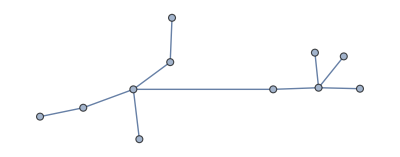
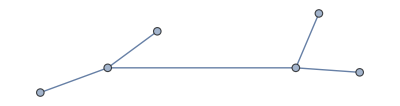
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
IsospectralPairs[treesten]  (* The suspects. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify  (* Testing multiplicities *)
```

{-64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k)),64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k))}

```mathematica
Finalisospectraltreesten={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* The checked trees with up to twelve vertices *)
```

Here we do it for a decorated square.

```mathematica
treesfromsquare=PendantEdgeAddAll[-Graphics-,6]; (* Here we create a square decorated with edges and trees. *)
```

Below are the checked isospectral sets from a decorated square. There is one triplet and the rest are pairs.

```mathematica
checkedsquarepairs=
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Here we do it for a decorated hexagon .

```mathematica
treesfromhexagon=PendantEdgeAddAll[-Graphics-,6];
```

Below are the checked decorated hexagon isospectral sets. I found one triplet and the rest are pairs.

```mathematica
checkedhexagonpairs={{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}.{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most six edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most five edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

## The following cells check the isospectrality of two selected pairs from the paper.

The following cell gives the vertex and edge scattering matrix for graph b): -Graphics-which is the isospectral partner of the loop graph when L1=L3=1/4 and L2=2/4 according to Pistol, arXiv.
It also computes ∑(k) following Berkolaiko which shows that graph b) has the same eigenfrequencies as graph a).

```mathematica
L1=L3=1/4;
L2=2/4;
Sv=({{0, -1/2, 1/2, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0}, {0, 1/2, 1/2, -1/2, 0, 1/2}, {0, 1/2, -1/2, 1/2, 0, 1/2}, {0, 1/2, 1/2, 1/2, 0, -1/2}, {0, 0, 0, 0, 1, 0}});
Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3)}});
Id=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k] (* The secular determinant *)

L1=1/2;L2=1/2;
Det[({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})-({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}).({{ⅇ^(ⅈ k L1), 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0}, {0, 0, 0, ⅇ^(ⅈ k L2)}})]//Simplify
DeterminantD[-Graphics-]//Simplify (* The same secular determinant apart from a factor which never gives a root *)
Solve[Sigma[k]==0,k]  (* The eigenfrequencies according to the handcalculated Sv and Se *)
GraphRoots[-Graphics-] (* The same eigenfrequencies according to my program. *)
```

(-1+ⅇ^(ⅈ k))^2

(-1+ⅇ^(ⅈ k))^2

DeterminantD[-Graphics-]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0},{k→-2 π},{k→2 π},{k→-2 ArcCos[-1/4]},{k→2 ArcCos[-1/4]}}

GraphRoots[-Graphics-]

The following cell shows that the graphs -Graphics-have the same secular determinant.

```mathematica
Subscript[L, 1]=1;
Sv=({{0, -1/3, 2/3, 0, 2/3, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 2/3, -1/3, 0, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 2/3, 2/3, 0, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1]), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 1])}})
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify

Subscript[L, 1]=1;Subscript[L, 2]=4;
Sv=({{0, -1/3, 2/3, 2/3}, {1, 0, 0, 0}, {0, 2/3, 2/3, -1/3}, {0, 2/3, -1/3, 2/3}});
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2])}});
Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify
```

1/3 (-1+ⅇ^(2 ⅈ k))^2 (3+7 ⅇ^(2 ⅈ k)+7 ⅇ^(4 ⅈ k)+3 ⅇ^(6 ⅈ k))

1/3 (-1+ⅇ^(2 ⅈ k))^2 (3+7 ⅇ^(2 ⅈ k)+7 ⅇ^(4 ⅈ k)+3 ⅇ^(6 ⅈ k))